ClearAll

SetDelayed::write: Tag Real in 0.02[n_] is Protected.

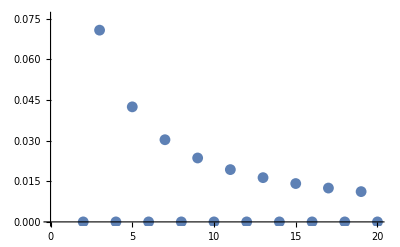

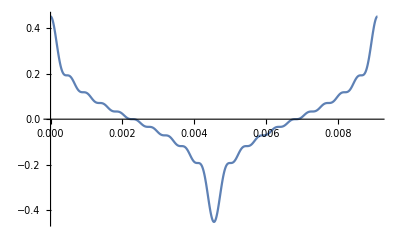

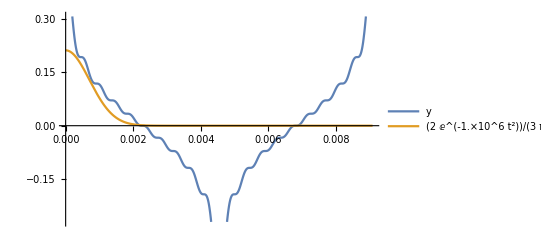

```mathematica
ClearAll

f=110; (* Frequency in hz, played*)
ω=Table[2*π*f*n, {n,1,20}];(*angular frequency of traveling wave*)
T =1/f;(*periodcity after some fiddling*)
ϕ = 0;(*phase shift , why not*)
A[n_]:=1/T Integrate[Cos[ω[[n]]*t]*Cos[π n t/T],{t,0,T}]; (*Coefficient formula*) 
B[n_]:=1/T Integrate[Cos[ω[[n]]*t]*Sin[π n t/T],{t,0,T}];
(*Coefficient formula*) 
B1=Table[Abs[B[n]],{n,1,20}];
(*Calculates n odd coefficients and stores in a table*) 
ListPlot[B1] (*Lists table in a graph of amplitudes*) 

g= (B1[[Ordering[B1,-1]]])*Exp[-(t^2)/.000001 +ϕ]; (*Filter function modeling wah effect, modeled from typical gaussian. Takes highest amplitude in fourier series and sets as own amplitude.*) 
y = ∑_(n=1)^(n=20) B1[[n]]*Cos[ω[[n]]*t+ϕ];
(*wave function containing amplitdues derived from the set frequency*) 

Plot[{y},{t,0,T},PlotLegends->"Expressions"](*graphs y function over t*) 
Plot[{y,g},{t,0,T},PlotLegends->"Expressions"](*graphs y function then overlays g over t*) 
Manipulate[Plot[{y*g },{t,0,T},PlotLegends->"Expressions"],{ω,0,T}]
(*graphs the product of the filter function and the frequency function and allows user to slide across frequency spectrum*******************NOTE: AM HAVING TROUBLE FINDING A COMPONENT THAT WILL SHIFT FUNCTION ACROSS SPECTRUM)
```